Práctica 2.2

1. Influencia del paso de Montecarlo. Realiza cinco simulaciones con los siguientes datos:

200  ngotas // 10 box // 10 boxz // red colocacion inicial (red o rnd) // 100000 intentos // 2.0 paso // 50 nbinz // 100 Nmed // 5 Nescr // 1.0 mg/kt

tomando los siguientes valores para el paso de Montecarlo: 0.1, 0.5, 1.0, 1.5 y 2.0.

• Representa la tasa de aceptación final en función del paso de Montecarlo. Explica el porqué de ese comportamiento.

| Paso | Tasa de aceptación
 | 0.1 | 0.908611
 | 0.5 | 0.579195
 | 1. | 0.375345
 | 1.5 | 0.267451
 | 2. | 0.200042

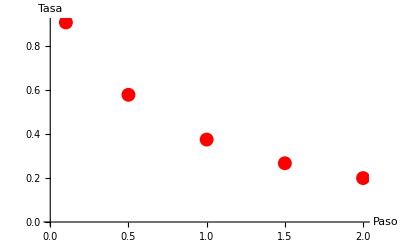

```mathematica
SetDirectory[NotebookDirectory[]];
paso=Import ["A1.txt","Table"];
TableForm[paso,TableHeadings->{{""},{"Paso","Tasa de aceptación"}}]
puntos=ListPlot[paso,PlotStyle-> {PointSize[0.025],RGBColor[1,0,0]},AxesLabel->{"Paso","Tasa"}]
List;
```

Al tratarse de una distribución normalizada la tasa de aceptación esta acotada entre los valores 0 y 1 (o si se prefiere entre el 0% y el 100%).  Por otro lado, y en base a la teoría, sabemos una tasa de aceptación optima ha de alejarse de los bordes, es decir, ha de oscilar entre 0.4 y 0.6. Esto es lógico pues en una simulación no es buena idea que se acepten o rechacen todos los movimientos propuestos para las partículas.

Cuando la tasa de aceptación es muy grande (paso pequeño) el movimiento propuesto para las partículas es mínimo. Las partículas apenas ven alteras su posición respecto de la inicial haciendo que la diferencia entre las energías del estado final e inicial sea negativa 

Si por el contrario la tasa de aceptación es pequeña (paso grande) el movimiento propuesto para las partículas es muy grande haciendo que se acepten muy pocos.

Cabe destacar que las tasas de aceptación parciales tienden a ser similares a las finales, no podría ser de otra manera pues de no ser así no alcanzaríamos el equilibrio.

• Ahora repite la simulación con paso 0.5 pero para N = 700. ¿Cuál es ahora la tasa de aceptación?

Para el paso 0.5 y N=700 la tasa de aceptación obtenida fue de 0.169725433 (~17%)

• Compara con la de N = 200. ¿Por qué son tan diferentes? 
En el caso de N=200 la tasa de aceptación es de 0.579195 (~58%). Este se debe a que al haber menos partículas en el mismo volumen la probabilidad de que estas choquen entre sí es significativamente menor y por tanto se aceptara un mayor número de movimientos, aumentando consigo la tasa de aceptación y justificando la discrepancia entre ambos casos.

• Una tasa de aceptación tan baja es un problema, porque indica que mi simulación es ineficiente, ya que está desperdiciando muchos intentos que luego no se aceptan. ¿Cómo se arreglaría?

A la vista de los resultados obtenidos una buena forma de solucionar una tasa de aceptación baja es aumentar el paso de Montecarlo hasta encontrar uno para el cual obtengamos un valor de la tasa de aceptación idónea.

2. Comparación con el gas ideal. Realiza una simulación con estos datos:

10  ngotas // 10 box // 10 boxz // rnd colocacion inicial (red o rnd) // 100000 intentos // 0.4 paso // 50 nbinz // 1000 Nmed // 5 Nescr // 1.0 mg/kt

Representa el perfil obtenido junto al perfil que tendría un gas ideal (la fórmula barométrica):

```mathematica
Subscript[ρ, GI][z_]:=N/A (m g)/(Subscript[k, b] T) (1-ⅇ^(-((m g L)/(Subscript[k, b] T))))^-1 ⅇ^(-((m g z)/(Subscript[k, b] T)));
```

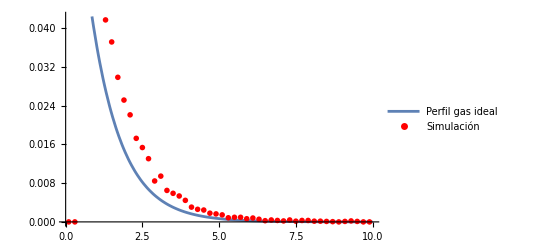

```mathematica
n=10;
A=100;
mgkt=1;
L=10;
Subscript[ρ, GI][z_]:=n/A *mgkt*(1-ⅇ^(-(mgkt*L)))^-1 ⅇ^(-(mgkt*z));
SetDirectory[NotebookDirectory[]];
paso1=Import ["binz0005","Table"];
a=Plot[{Subscript[ρ, GI][z]},{z,0,10}, PlotLegends->{"Perfil gas ideal"}];
grafperfil=ListPlot[paso1,PlotStyle-> {PointSize[0.01],RGBColor[1,0,0]},PlotRange-> All,PlotLegends->{"Simulación"}];
Show[a, grafperfil]
```

Antes de nada, ¿qué pasa en el bin que corresponde a z = 0,5 σ? ¿Cómo podría evitarse?

Para este apartado nuestros datos de entrada son boxz=10 y nbinz=50, luego el tamaño de nuestros binesz es tbin=boxz/nbinz=10/50=0.2. Entonces nos encontramos que el binz que del intervalo [0,0.2] está completamente vacío porque una de las condiciones de nuestro programa es que las bolas que estén por debajo de z=0.5 σ se descartan para que todas las que midamos estén por encima del suelo. Lo mismo pasa en el intervalo [0.2,0.4]. En el siguiente intervalo [0.4,0.6] comienzan a aceptarse bolas pero sólo las que están por encima de 0.5, por eso este punto no sigue la misma tendencia que el resto. Una forma de evitarse es cambiando la altura de la caja o el número de bines en esta dirección. Por ejemplo, si cambiamos nbinz=40, ahora uno de los intervalos comenzará en  z = 0.5 σ solucionando el problema

¿Por qué ambos perfiles se parecen tanto? 

Ambos perfiles se parecen porque la física que hay detrás de ellos es equivalente. Nuestro programa es una simulación en un cierto volumen  del comportamiento de un gas ideal  tridimensional en presencia de un campo gravitatorio. La fórmula barométrica es esencialmente lo mismo pues trata de simular la distribución de las moléculas de gas en la atmósfera terrestre (teniendo en cuenta la gravedad) y ver como varía esta en función de la altitud.

¿Por qué parecen desplazadas?

Podemos ver que los puntos que corresponden a la simulación están por encima del perfil del gas ideal.  La distribución teórica abarca todo el espacio desde cero a la altura de la caja (10 en este caso) mientas que la simulación las partículas tiene un radio y como hemos dicho antes no pueden estar por debajo de la posición  z=0.5 σ, entonces las partículas que en la teórica están en el intervalo [0,0.5], zona de mayor densidad, ahora tienen que redistribuirse entre el espacio permitido en la simulación, aumentando la densidad de este.

3. Efecto del campo externo. Realiza tres simulaciones con estos datos:

400 ngotas // 10 box // 10 boxz // red colocacion inicial (red o rnd) // 10000 intentos // 0.2 paso // 40 nbinz // 100 Nmed // 5 Nescr // 0.0 mg/kt

variando la intensidad del campo externo: mg/kbT = 0, 1 y 5. Describe los resultados y explica las diferencias.

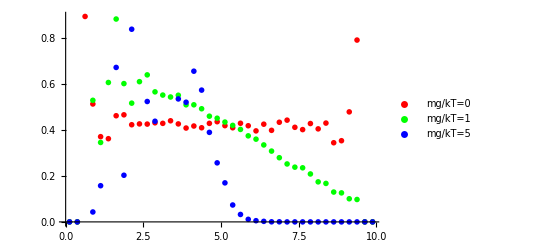

Leídas 400 esferas

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
SetDirectory[NotebookDirectory[]];
perfil0=Import ["binz0","Table"];
perfil1=Import ["binz1","Table"];
perfil5=Import ["binz5","Table"];
centrosini0=Import ["pos0000.0","Table"];
centrosfin0=Import ["pos9999.0","Table"];
centrosfin1=Import ["pos9999.1","Table"];
centrosfin5=Import ["pos9999.5","Table"];
grafperfil0=ListPlot[perfil0,PlotStyle-> {PointSize[0.01],RGBColor[1,0,0]},PlotRange-> All,PlotLegends->{"mg/kT=0"}];
grafperfil1=ListPlot[perfil1,PlotStyle-> {PointSize[0.01],RGBColor[0,1,0]},PlotRange-> All,PlotLegends->{"mg/kT=1"}];
grafperfil5=ListPlot[perfil5,PlotStyle-> {PointSize[0.01],RGBColor[0,0,1]},PlotRange-> All,PlotLegends->{"mg/kT=5"}];
Show[grafperfil0, grafperfil1, grafperfil5]
nb0=Length[centrosini0];
Print["Leídas ",nb0," esferas"];
bolasini0=Table[Sphere[centrosini0[[i]],0.5],{i,1,nb0}];
gbi0=Graphics3D[bolasini0,Axes->True,LabelStyle->{FontFamily->"Helvetica",FontSize->16},AxesLabel->{"x","y","z"},PlotRange->{All,All,{0,10}},PlotLabel->"• Posición inicial     (1)"] 
bolasfin0=Table[Sphere[centrosfin0[[i]],0.5],{i,1,nb0}];
gbf0=Graphics3D[bolasfin0, Axes->True,LabelStyle->{FontFamily->"Helvetica",FontSize->16},AxesLabel->{"x","y","z"},PlotRange ->{All,All, {0,10}}, PlotLabel->"• Posición a (m g)/k_b = 0     (2)"]
bolasfin1=Table[Sphere[centrosfin1[[i]],0.5],{i,1,nb0}];
gbf1=Graphics3D[bolasfin1, Axes->True,LabelStyle->{FontFamily->"Helvetica",FontSize->16},AxesLabel->{"x","y","z"},PlotRange ->{All,All, {0,10}},PlotLabel->"• Posición a (m g)/k_b = 1     (3)"]
bolasfin5=Table[Sphere[centrosfin5[[i]],0.5],{i,1,nb0}];
gbf5=Graphics3D[bolasfin5, Axes->True,LabelStyle->{FontFamily->"Helvetica",FontSize->16},AxesLabel->{"x","y","z"},PlotRange ->{All,All, {0,10}},PlotLabel->"• Posición a (m g)/k_b = 5     (4)"]
```